```mathematica
datakow10n1ow=Import["/localscratch/asourpis/metadata_MOGON/ff_evalution/kows/10/rdf_n1_ow.xvg","Table"]//Drop[#,25]&;
datakow50n1ow=Import["/localscratch/asourpis/metadata_MOGON/ff_evalution/kows/50/rdf_n1_ow.xvg","Table"]//Drop[#,25]&;
datakow90n1ow=Import["/localscratch/asourpis/metadata_MOGON/ff_evalution/kows/90/rdf_n1_ow.xvg","Table"]//Drop[#,25]&;
dataniki10n1ow=Import["/localscratch/asourpis/metadata_MOGON/ff_evalution/niki/10/rdf_n1_ow.xvg","Table"]//Drop[#,25]&;
dataniki50n1ow=Import["/localscratch/asourpis/metadata_MOGON/ff_evalution/niki/50/rdf_n1_ow.xvg","Table"]//Drop[#,25]&;
dataniki90n1ow=Import["/localscratch/asourpis/metadata_MOGON/ff_evalution/niki/90/rdf_n1_ow.xvg","Table"]//Drop[#,25]&;
datagrab10n1ow=Import["/localscratch/asourpis/metadata_MOGON/ff_evalution/grab/10/rdf_n1_ow.xvg","Table"]//Drop[#,25]&;
datagrab50n1ow=Import["/localscratch/asourpis/metadata_MOGON/ff_evalution/grab/50/rdf_n1_ow.xvg","Table"]//Drop[#,25]&;
datagrab90n1ow=Import["/localscratch/asourpis/metadata_MOGON/ff_evalution/grab/90/rdf_n1_ow.xvg","Table"]//Drop[#,25]&;
datakalu10n1ow=Import["/localscratch/asourpis/metadata_MOGON/ff_evalution/kalu/10/rdf_n1_ow.xvg","Table"]//Drop[#,25]&;
datakalu50n1ow=Import["/localscratch/asourpis/metadata_MOGON/ff_evalution/kalu/50/rdf_n1_ow.xvg","Table"]//Drop[#,25]&;
datakalu90n1ow=Import["/localscratch/asourpis/metadata_MOGON/ff_evalution/kalu/90/rdf_n1_ow.xvg","Table"]//Drop[#,25]&;
```

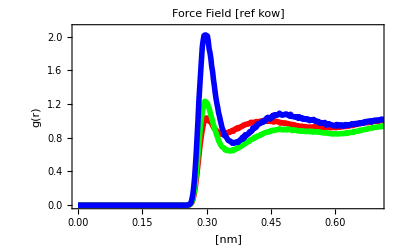

```mathematica
g1=ListLinePlot[{datakow10n1ow,datakow50n1ow,datakow90n1ow},PlotRange->{{0.0,0.7},{0,2.1}},Frame->True,FrameLabel->{"[nm]","g(r)"},FrameStyle->Directive[Gray,FontSize->10],PlotStyle->{{Red,Thickness[0.01]},{Green,Thickness[0.01]},{Blue,Thickness[0.01]}},FrameTicksStyle->{Thick,Thick},LabelStyle->Directive[Gray,Bold],PlotLabel->"Force Field [ref kow]"]
```

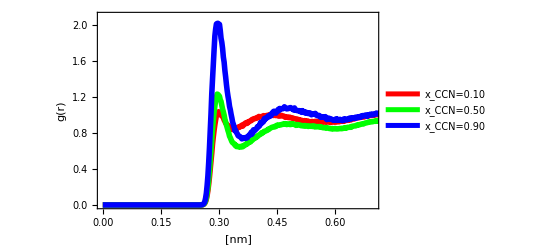

-Graphics-

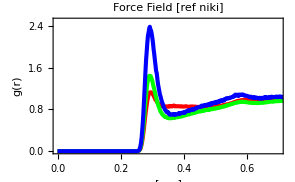

```mathematica
g2=ListLinePlot[{dataniki10n1ow,dataniki50n1ow,dataniki90n1ow},Frame->True,PlotRange->{{0.0,0.7},{0,2.5}},Frame->True,FrameLabel->{"[nm]","g(r)"},FrameStyle->Directive[Gray,FontSize->10],PlotStyle->{{Red,Thickness[0.01]},{Green,Thickness[0.01]},{Blue,Thickness[0.01]}},FrameTicksStyle->{Thick,Thick},LabelStyle->Directive[Gray,Bold],PlotLabel->"Force Field [ref niki]"]
```

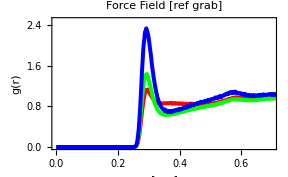

```mathematica
g3=ListLinePlot[{datagrab10n1ow,datagrab50n1ow,datagrab90n1ow},Frame->True,PlotRange->{{0.0,0.7},{0,2.5}},Frame->True,FrameLabel->{"[nm]","g(r)"},FrameStyle->Directive[Gray,FontSize->10],PlotStyle->{{Red,Thickness[0.01]},{Green,Thickness[0.01]},{Blue,Thickness[0.01]}},FrameTicksStyle->{Thick,Thick},LabelStyle->Directive[Gray,Bold],PlotLabel->"Force Field [ref grab]"]
```

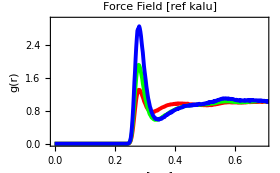

```mathematica
g4=ListLinePlot[{datakalu10n1ow,datakalu50n1ow,datakalu90n1ow},Frame->True,PlotRange->{{0.0,0.7},{0,3.0}},Frame->True,FrameLabel->{"[nm]","g(r)"},FrameStyle->Directive[Gray,FontSize->10],PlotStyle->{{Red,Thickness[0.01]},{Green,Thickness[0.01]},{Blue,Thickness[0.01]}},FrameTicksStyle->{Thick,Thick},LabelStyle->Directive[Gray,Bold],PlotLabel->"Force Field [ref kalu]"]
```

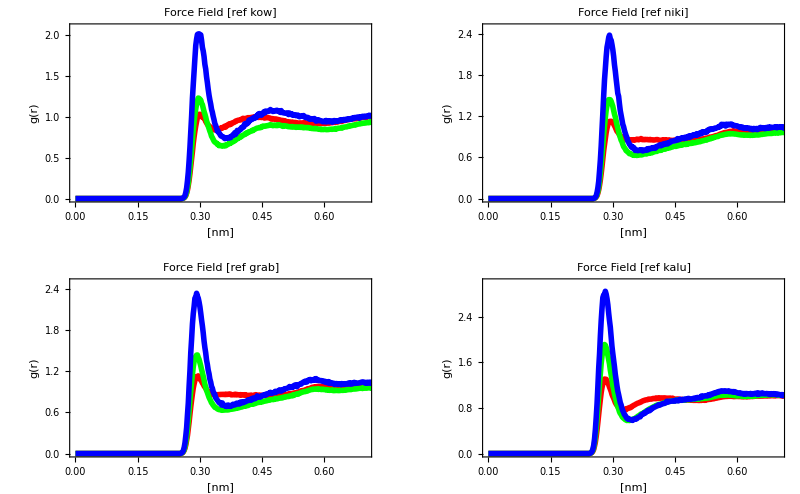

```mathematica
GraphicsGrid[{{g1,g2},{g3,g4}}]
```

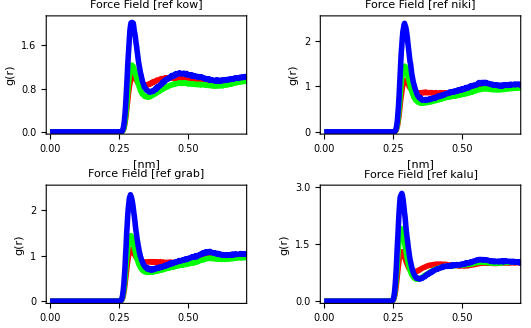
1/-Graphics-Ab-initio [ref.]
-Graphics-

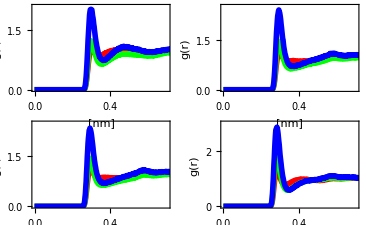
```mathematica
-Graphics-/-Graphics-
```

1/-Graphics- -Graphics-

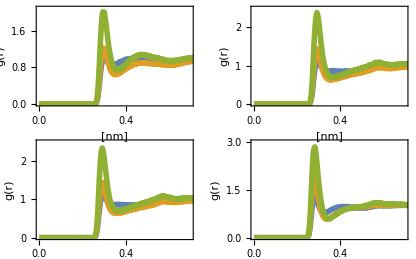
```mathematica
-Graphics-/-Graphics-
```

1/-Graphics- -Graphics-

-Graphics-

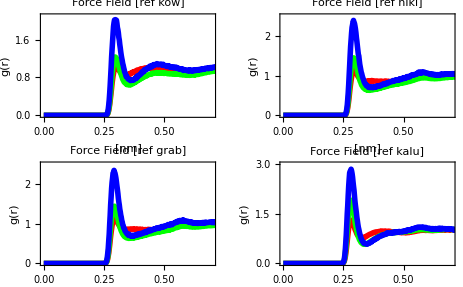
```mathematica
-Graphics-/{{Ab-initio [ref.]}, {-Graphics-}}
```

```mathematica
datakow10n1hw=Import["/localscratch/asourpis/metadata_MOGON/ff_evalution/kows/10/rdf_n1_hw.xvg","Table"]//Drop[#,25]&;
datakow50n1hw=Import["/localscratch/asourpis/metadata_MOGON/ff_evalution/kows/50/rdf_n1_hw.xvg","Table"]//Drop[#,25]&;
datakow90n1hw=Import["/localscratch/asourpis/metadata_MOGON/ff_evalution/kows/90/rdf_n1_hw.xvg","Table"]//Drop[#,25]&;
dataniki10n1hw=Import["/localscratch/asourpis/metadata_MOGON/ff_evalution/niki/10/rdf_n1_hw.xvg","Table"]//Drop[#,25]&;
dataniki50n1hw=Import["/localscratch/asourpis/metadata_MOGON/ff_evalution/niki/50/rdf_n1_hw.xvg","Table"]//Drop[#,25]&;
dataniki90n1hw=Import["/localscratch/asourpis/metadata_MOGON/ff_evalution/niki/90/rdf_n1_hw.xvg","Table"]//Drop[#,25]&;
datagrab10n1hw=Import["/localscratch/asourpis/metadata_MOGON/ff_evalution/grab/10/rdf_n1_hw.xvg","Table"]//Drop[#,25]&;
datagrab50n1hw=Import["/localscratch/asourpis/metadata_MOGON/ff_evalution/grab/50/rdf_n1_hw.xvg","Table"]//Drop[#,25]&;
datagrab90n1hw=Import["/localscratch/asourpis/metadata_MOGON/ff_evalution/grab/90/rdf_n1_hw.xvg","Table"]//Drop[#,25]&;
datakalu10n1hw=Import["/localscratch/asourpis/metadata_MOGON/ff_evalution/kalu/10/rdf_n1_hw.xvg","Table"]//Drop[#,25]&;
datakalu50n1hw=Import["/localscratch/asourpis/metadata_MOGON/ff_evalution/kalu/50/rdf_n1_hw.xvg","Table"]//Drop[#,25]&;
datakalu90n1hw=Import["/localscratch/asourpis/metadata_MOGON/ff_evalution/kalu/90/rdf_n1_hw.xvg","Table"]//Drop[#,25]&;
```

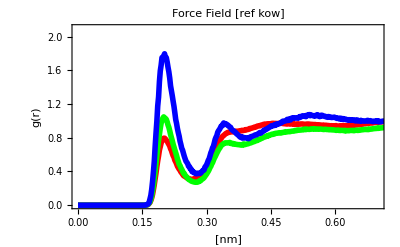

```mathematica
g1=ListLinePlot[{datakow10n1hw,datakow50n1hw,datakow90n1hw},PlotRange->{{0.0,0.7},{0,2.1}},Frame->True,FrameLabel->{"[nm]","g(r)"},FrameStyle->Directive[Gray,FontSize->10],PlotStyle->{{Red,Thickness[0.01]},{Green,Thickness[0.01]},{Blue,Thickness[0.01]}},FrameTicksStyle->{Thick,Thick},LabelStyle->Directive[Gray,Bold],PlotLabel->"Force Field [ref kow]"]
```

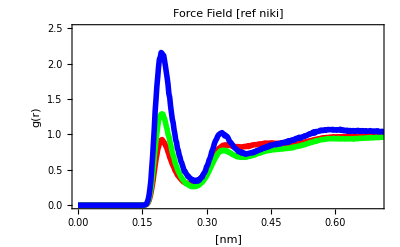

```mathematica
g2=ListLinePlot[{dataniki10n1hw,dataniki50n1hw,dataniki90n1hw},Frame->True,PlotRange->{{0.0,0.7},{0,2.5}},Frame->True,FrameLabel->{"[nm]","g(r)"},FrameStyle->Directive[Gray,FontSize->10],PlotStyle->{{Red,Thickness[0.01]},{Green,Thickness[0.01]},{Blue,Thickness[0.01]}},FrameTicksStyle->{Thick,Thick},LabelStyle->Directive[Gray,Bold],PlotLabel->"Force Field [ref niki]"]
```

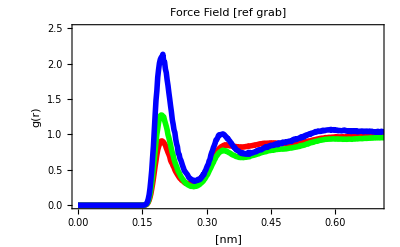

```mathematica
g3=ListLinePlot[{datagrab10n1hw,datagrab50n1hw,datagrab90n1hw},Frame->True,PlotRange->{{0.0,0.7},{0,2.5}},Frame->True,FrameLabel->{"[nm]","g(r)"},FrameStyle->Directive[Gray,FontSize->10],PlotStyle->{{Red,Thickness[0.01]},{Green,Thickness[0.01]},{Blue,Thickness[0.01]}},FrameTicksStyle->{Thick,Thick},LabelStyle->Directive[Gray,Bold],PlotLabel->"Force Field [ref grab]"]
```

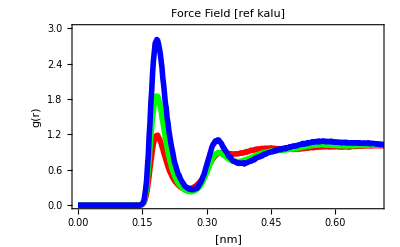

```mathematica
g4=ListLinePlot[{datakalu10n1hw,datakalu50n1hw,datakalu90n1hw},Frame->True,PlotRange->{{0.0,0.7},{0,3.0}},Frame->True,FrameLabel->{"[nm]","g(r)"},FrameStyle->Directive[Gray,FontSize->10],PlotStyle->{{Red,Thickness[0.01]},{Green,Thickness[0.01]},{Blue,Thickness[0.01]}},FrameTicksStyle->{Thick,Thick},LabelStyle->Directive[Gray,Bold],PlotLabel->"Force Field [ref kalu]"]
```

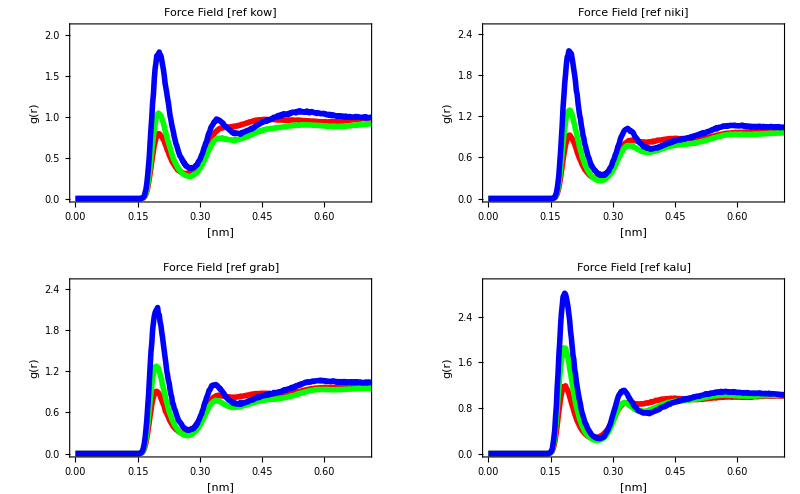

```mathematica
GraphicsGrid[{{g1,g2},{g3,g4}}]
```

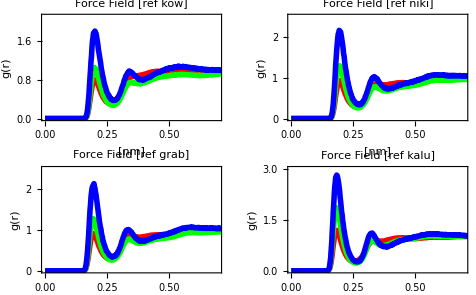
```mathematica
-Graphics-/{{Ab-initio [ref.]}, {-Graphics-}}-Graphics-
```

Final Plots

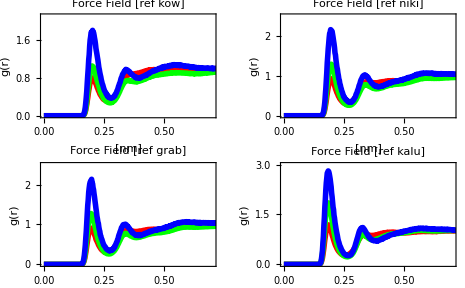
```mathematica
-Graphics-/{{Ab-initio [ref.]}, {-Graphics-}}
```

```mathematica
-Graphics-/{{Ab-initio [ref.]}, {-Graphics-}}
```

```mathematica
datakow10owow=Import["/localscratch/asourpis/metadata_MOGON/ff_evalution/kows/10/rdf_ow_ow.xvg","Table"]//Drop[#,25]&;
datakow50owow=Import["/localscratch/asourpis/metadata_MOGON/ff_evalution/kows/50/rdf_ow_ow.xvg","Table"]//Drop[#,25]&;
datakow90owow=Import["/localscratch/asourpis/metadata_MOGON/ff_evalution/kows/90/rdf_ow_ow.xvg","Table"]//Drop[#,25]&;
```

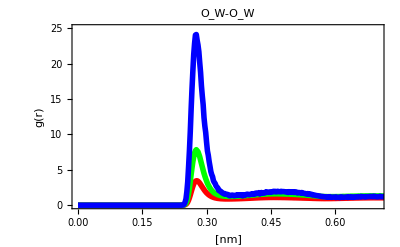

```mathematica
g1owow=ListLinePlot[{datakow10owow,datakow50owow,datakow90owow},PlotRange->{{0.0,0.7},{0,25}},Frame->True,FrameLabel->{"[nm]","g(r)"},FrameStyle->Directive[Gray,FontSize->10],PlotStyle->{{Red,Thickness[0.01]},{Green,Thickness[0.01]},{Blue,Thickness[0.01]}},FrameTicksStyle->{Thick,Thick},LabelStyle->Directive[Gray,Bold],PlotLabel->"O_W-O_W"]
```

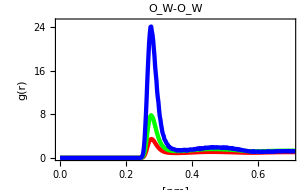

-Graphics-

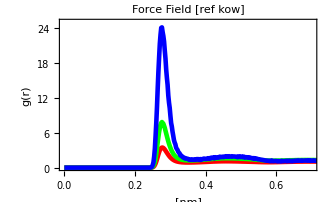

-Graphics-

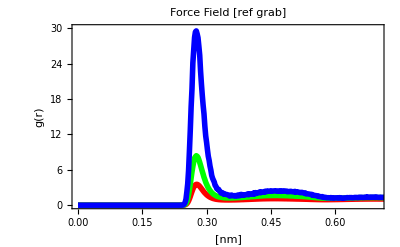

```mathematica
datagrab10owow=Import["/localscratch/asourpis/metadata_MOGON/ff_evalution/grab/10/rdf_ow_ow.xvg","Table"]//Drop[#,25]&;
datagrab50owow=Import["/localscratch/asourpis/metadata_MOGON/ff_evalution/grab/50/rdf_ow_ow.xvg","Table"]//Drop[#,25]&;
datagrab90owow=Import["/localscratch/asourpis/metadata_MOGON/ff_evalution/grab/90/rdf_ow_ow.xvg","Table"]//Drop[#,25]&;
g2owow=ListLinePlot[{datagrab10owow,datagrab50owow,datagrab90owow},PlotRange->{{0.0,0.7},{0,30}},Frame->True,FrameLabel->{"[nm]","g(r)"},FrameStyle->Directive[Gray,FontSize->10],PlotStyle->{{Red,Thickness[0.01]},{Green,Thickness[0.01]},{Blue,Thickness[0.01]}},FrameTicksStyle->{Thick,Thick},LabelStyle->Directive[Gray,Bold],PlotLabel->"Force Field [ref grab]"]
```

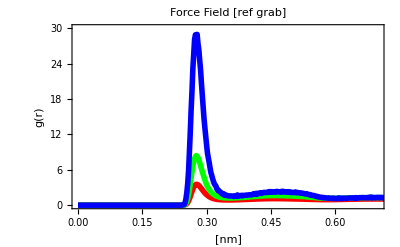

```mathematica
dataniki10owow=Import["/localscratch/asourpis/metadata_MOGON/ff_evalution/niki/10/rdf_ow_ow.xvg","Table"]//Drop[#,25]&;
dataniki50owow=Import["/localscratch/asourpis/metadata_MOGON/ff_evalution/niki/50/rdf_ow_ow.xvg","Table"]//Drop[#,25]&;
dataniki90owow=Import["/localscratch/asourpis/metadata_MOGON/ff_evalution/niki/90/rdf_ow_ow.xvg","Table"]//Drop[#,25]&;
g3owow=ListLinePlot[{dataniki10owow,dataniki50owow,dataniki90owow},PlotRange->{{0.0,0.7},{0,30}},Frame->True,FrameLabel->{"[nm]","g(r)"},FrameStyle->Directive[Gray,FontSize->10],PlotStyle->{{Red,Thickness[0.01]},{Green,Thickness[0.01]},{Blue,Thickness[0.01]}},FrameTicksStyle->{Thick,Thick},LabelStyle->Directive[Gray,Bold],PlotLabel->"Force Field [ref grab]"]
```

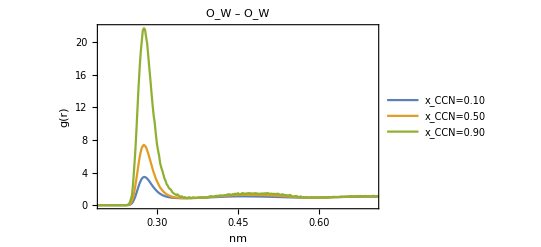

```mathematica
datakalu10owow=Import["/localscratch/asourpis/metadata_MOGON/ff_evalution/kalu/10/rdf_ow_ow.xvg","Table"]//Drop[#,25]&;
datakalu50owow=Import["/localscratch/asourpis/metadata_MOGON/ff_evalution/kalu/50/rdf_ow_ow.xvg","Table"]//Drop[#,25]&;
datakalu90owow=Import["/localscratch/asourpis/metadata_MOGON/ff_evalution/kalu/90/rdf_ow_ow.xvg","Table"]//Drop[#,25]&;
g1owow=ListLinePlot[{datakalu10owow,datakalu50owow,datakalu90owow},PlotRange->{{0.2,0.7},All},Frame->True,FrameLabel->{"nm","g(r)"},Filling->{Top,Bottom,0.2},PlotStyle->{PointSize[0.02]},
LabelStyle->{FontFamily->"Serif",12},BaseStyle->{FontFamily->"Serif"},FrameStyle->Directive[Black,Thick],Frame->True,PlotStyle->{Blue, Red,Green},PlotRange->{{0,0.7},All},PlotLabel->Style["O_W – O_W",Black,24,FontFamily->"Serif"],PlotLegends->{"x_CCN=0.10","x_CCN=0.50","x_CCN=0.90"}]
```

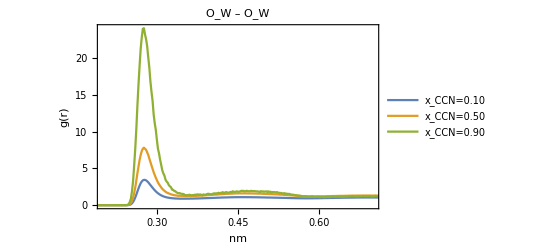

```mathematica
datakows10owow=Import["/localscratch/asourpis/metadata_MOGON/ff_evalution/kows/10/rdf_ow_ow.xvg","Table"]//Drop[#,25]&;
datakows50owow=Import["/localscratch/asourpis/metadata_MOGON/ff_evalution/kows/50/rdf_ow_ow.xvg","Table"]//Drop[#,25]&;
datakows90owow=Import["/localscratch/asourpis/metadata_MOGON/ff_evalution/kows/90/rdf_ow_ow.xvg","Table"]//Drop[#,25]&;
g2owow=ListLinePlot[{datakows10owow,datakows50owow,datakows90owow},PlotRange->{{0.2,0.7},All},Frame->True,FrameLabel->{"nm","g(r)"},Filling->{Top,Bottom,0.2},PlotStyle->{PointSize[0.02]},
LabelStyle->{FontFamily->"Serif",12},BaseStyle->{FontFamily->"Serif"},FrameStyle->Directive[Black,Thick],Frame->True,PlotStyle->{Blue, Red,Green},PlotRange->{{0,0.7},All},PlotLabel->Style["O_W – O_W",Black,24,FontFamily->"Serif"],PlotLegends->{"x_CCN=0.10","x_CCN=0.50","x_CCN=0.90"}]
```

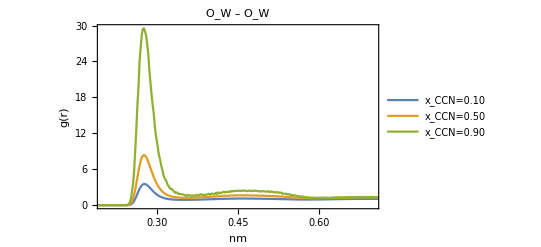

```mathematica
datagrab10owow=Import["/localscratch/asourpis/metadata_MOGON/ff_evalution/grab/10/rdf_ow_ow.xvg","Table"]//Drop[#,25]&;
datagrab50owow=Import["/localscratch/asourpis/metadata_MOGON/ff_evalution/grab/50/rdf_ow_ow.xvg","Table"]//Drop[#,25]&;
datagrab90owow=Import["/localscratch/asourpis/metadata_MOGON/ff_evalution/grab/90/rdf_ow_ow.xvg","Table"]//Drop[#,25]&;
g3owow=ListLinePlot[{datagrab10owow,datagrab50owow,datagrab90owow},PlotRange->{{0.2,0.7},All},Frame->True,FrameLabel->{"nm","g(r)"},Filling->{Top,Bottom,0.2},PlotStyle->{PointSize[0.02]},
LabelStyle->{FontFamily->"Serif",12},BaseStyle->{FontFamily->"Serif"},FrameStyle->Directive[Black,Thick],Frame->True,PlotStyle->{Blue, Red,Green},PlotRange->{{0,0.7},All},PlotLabel->Style["O_W – O_W",Black,24,FontFamily->"Serif"],PlotLegends->{"x_CCN=0.10","x_CCN=0.50","x_CCN=0.90"}]
```

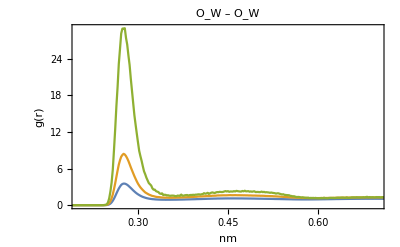

```mathematica
dataniki10owow=Import["/localscratch/asourpis/metadata_MOGON/ff_evalution/niki/10/rdf_ow_ow.xvg","Table"]//Drop[#,25]&;
dataniki50owow=Import["/localscratch/asourpis/metadata_MOGON/ff_evalution/niki/50/rdf_ow_ow.xvg","Table"]//Drop[#,25]&;
dataniki90owow=Import["/localscratch/asourpis/metadata_MOGON/ff_evalution/niki/90/rdf_ow_ow.xvg","Table"]//Drop[#,25]&;
g4owow=ListLinePlot[{dataniki10owow,dataniki50owow,dataniki90owow},PlotRange->{{0.2,0.7},All},Frame->True,FrameLabel->{"nm","g(r)"},Filling->{Top,Bottom,0.2},PlotStyle->{PointSize[0.02]},
LabelStyle->{FontFamily->"Serif",12},BaseStyle->{FontFamily->"Serif"},FrameStyle->Directive[Black,Thick],Frame->True,PlotStyle->{Blue, Red,Green},PlotRange->{{0,0.7},All},PlotLabel->Style["O_W – O_W",Black,24,FontFamily->"Serif"],PlotLegends->"Expressions"]
```

```mathematica
GraphicsGrid[{{g1owow,g2owow},{g3owow,g4owow}}]
```

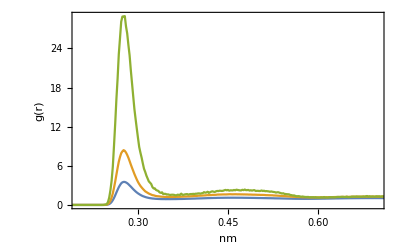

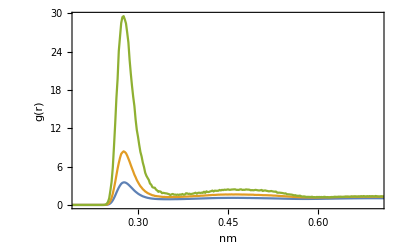

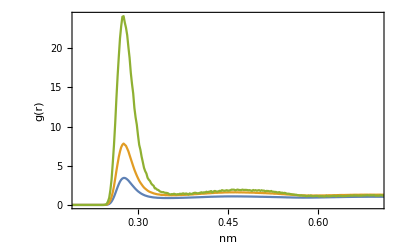

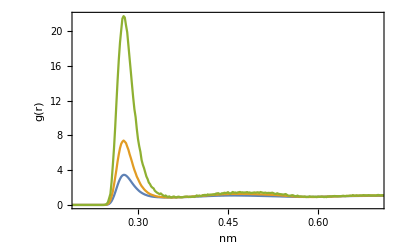

```mathematica
g4owow=ListLinePlot[{dataniki10owow,dataniki50owow,dataniki90owow},PlotRange->{{0.2,0.7},All},Frame->True,FrameLabel->{"nm","g(r)"},Filling->{Top,Bottom,0.2},PlotStyle->{PointSize[0.02]},
LabelStyle->{FontFamily->"Serif",12},BaseStyle->{FontFamily->"Serif"},FrameStyle->Directive[Black,Thick],Frame->True,PlotStyle->{Blue, Red,Green},PlotRange->{{0,0.7},All}]
g3owow=ListLinePlot[{datagrab10owow,datagrab50owow,datagrab90owow},PlotRange->{{0.2,0.7},All},Frame->True,FrameLabel->{"nm","g(r)"},Filling->{Top,Bottom,0.2},PlotStyle->{PointSize[0.02]},
LabelStyle->{FontFamily->"Serif",12},BaseStyle->{FontFamily->"Serif"},FrameStyle->Directive[Black,Thick],Frame->True,PlotStyle->{Blue, Red,Green},PlotRange->{{0,0.7},All}]
g2owow=ListLinePlot[{datakows10owow,datakows50owow,datakows90owow},PlotRange->{{0.2,0.7},All},Frame->True,FrameLabel->{"nm","g(r)"},Filling->{Top,Bottom,0.2},PlotStyle->{PointSize[0.02]},
LabelStyle->{FontFamily->"Serif",12},BaseStyle->{FontFamily->"Serif"},FrameStyle->Directive[Black,Thick],Frame->True,PlotStyle->{Blue, Red,Green},PlotRange->{{0,0.7},All}]
g1owow=ListLinePlot[{datakalu10owow,datakalu50owow,datakalu90owow},PlotRange->{{0.2,0.7},All},Frame->True,FrameLabel->{"nm","g(r)"},Filling->{Top,Bottom,0.2},PlotStyle->{PointSize[0.02]},
LabelStyle->{FontFamily->"Serif",12},BaseStyle->{FontFamily->"Serif"},FrameStyle->Directive[Black,Thick],Frame->True,PlotStyle->{Blue, Red,Green},PlotRange->{{0,0.7},All}]
```

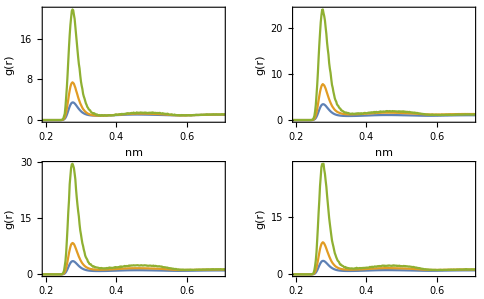

```mathematica
GraphicsGrid[{{g1owow,g2owow},{g3owow,g4owow}}]
```

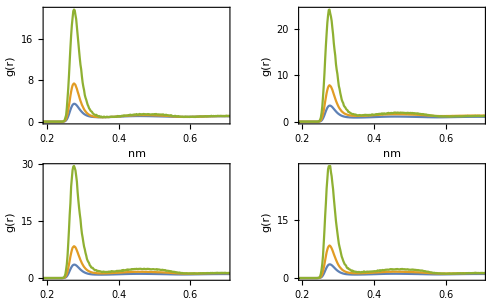

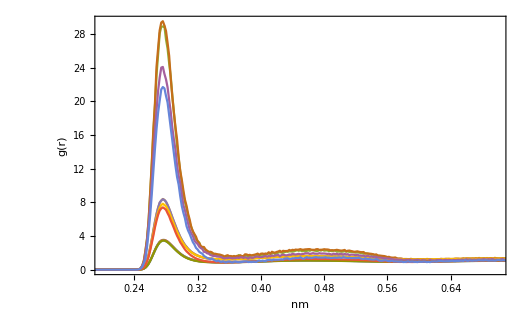

```mathematica
g4owow=ListLinePlot[{dataniki10owow,dataniki50owow,dataniki90owow,datagrab10owow,datagrab50owow,datagrab90owow,datakows10owow,datakows50owow,datakows90owow,datakalu10owow,datakalu50owow,datakalu90owow},PlotRange->{{0.2,0.7},All},Frame->True,FrameLabel->{"nm","g(r)"},Filling->{Top,Bottom,0.2},PlotStyle->{PointSize[0.02]},
LabelStyle->{FontFamily->"Serif",12},BaseStyle->{FontFamily->"Serif"},FrameStyle->Directive[Black,Thick],Frame->True,PlotStyle->{Blue, Red,Green,Yellow,Black},PlotRange->{{0,0.7},All}]
```